```mathematica
nph=100;
ns=1;
Δ=π;
(*rk here represents Subscript[r, k],magnitude of input state coefficient*)
r=Table[Table[Symbol["r"<>ToString[k]<>"s"<>ToString[l]],{k,0,nph}],{l,1,ns}];
(*θk here represents Subscript[θ, k],real phase of input state coefficient(exponent)*)
θ=Table[Table[Symbol["θ"<>ToString[k]<>"s"<>ToString[l]],{k,0,nph}],{l,1,ns}];
```

### Gaussian State c_p≃0.14, ρ≃c_p Δ/N

```mathematica
PlugG1SBS[]:=
Block[{},Clear[ρ3];
ρ3 = Table[Symbol["ρ3s"<>ToString[n]],{n,1,ns}];
Table[ρ3[[n]]=0.16Δ/nph;,{n,1,ns}];
ψG1r =Table[Table[(E^(-ρ3[[n]](k-nph/2)^2))/(√(∑_(kprime=0)^nph (E^(-ρ3[[n]](kprime-nph/2)^2))^2)),{k,0,nph}],{n,1,ns}];
ψG1θ=Table[Table[ k (π/2),{k,0,nph}],{n,1,ns}];
substlistG1r=Table[Table[r[[n,i]]-> ψG1r[[n,i]],{i,1,nph+1}],{n,1,ns}];
substlistG1θ = Table[Table[θ[[n,i]]-> ψG1θ[[n,i]],{i,1,nph+1}],{n,1,ns}];
substlistG1= Flatten[{substlistG1θ,substlistG1r}];
(*finalVarianceG1=finalVariance/.substlistG1;*)
(*Print[OptimalVarianceQG2];*)
(*this prints out optimized ρ and ρprime values*)
(*finalVarianceQG2[[2]]*)
(*Print[substlistG1];*)
(*This returns the state to be plugged in*)
Return[substlistG1];];
```

```mathematica
plotGaussian=PlugG1SBS[]
```

{θ0s1→0,θ1s1→π/2,θ2s1→π,θ3s1→(3 π)/2,θ4s1→2 π,θ5s1→(5 π)/2,θ6s1→3 π,θ7s1→(7 π)/2,θ8s1→4 π,θ9s1→(9 π)/2,θ10s1→5 π,θ11s1→(11 π)/2,θ12s1→6 π,θ13s1→(13 π)/2,θ14s1→7 π,θ15s1→(15 π)/2,θ16s1→8 π,θ17s1→(17 π)/2,θ18s1→9 π,θ19s1→(19 π)/2,θ20s1→10 π,θ21s1→(21 π)/2,θ22s1→11 π,θ23s1→(23 π)/2,θ24s1→12 π,θ25s1→(25 π)/2,θ26s1→13 π,θ27s1→(27 π)/2,θ28s1→14 π,θ29s1→(29 π)/2,θ30s1→15 π,θ31s1→(31 π)/2,θ32s1→16 π,θ33s1→(33 π)/2,θ34s1→17 π,θ35s1→(35 π)/2,θ36s1→18 π,θ37s1→(37 π)/2,θ38s1→19 π,θ39s1→(39 π)/2,θ40s1→20 π,θ41s1→(41 π)/2,θ42s1→21 π,θ43s1→(43 π)/2,θ44s1→22 π,θ45s1→(45 π)/2,θ46s1→23 π,θ47s1→(47 π)/2,θ48s1→24 π,θ49s1→(49 π)/2,θ50s1→25 π,θ51s1→(51 π)/2,θ52s1→26 π,θ53s1→(53 π)/2,θ54s1→27 π,θ55s1→(55 π)/2,θ56s1→28 π,θ57s1→(57 π)/2,θ58s1→29 π,θ59s1→(59 π)/2,θ60s1→30 π,θ61s1→(61 π)/2,θ62s1→31 π,θ63s1→(63 π)/2,θ64s1→32 π,θ65s1→(65 π)/2,θ66s1→33 π,θ67s1→(67 π)/2,θ68s1→34 π,θ69s1→(69 π)/2,θ70s1→35 π,θ71s1→(71 π)/2,θ72s1→36 π,θ73s1→(73 π)/2,θ74s1→37 π,θ75s1→(75 π)/2,θ76s1→38 π,θ77s1→(77 π)/2,θ78s1→39 π,θ79s1→(79 π)/2,θ80s1→40 π,θ81s1→(81 π)/2,θ82s1→41 π,θ83s1→(83 π)/2,θ84s1→42 π,θ85s1→(85 π)/2,θ86s1→43 π,θ87s1→(87 π)/2,θ88s1→44 π,θ89s1→(89 π)/2,θ90s1→45 π,θ91s1→(91 π)/2,θ92s1→46 π,θ93s1→(93 π)/2,θ94s1→47 π,θ95s1→(95 π)/2,θ96s1→48 π,θ97s1→(97 π)/2,θ98s1→49 π,θ99s1→(99 π)/2,θ100s1→50 π,r0s1→8.29434×10^-7,r1s1→1.36427×10^-6,r2s1→2.22152×10^-6,r3s1→3.58126×10^-6,r4s1→5.71551×10^-6,r5s1→9.03042×10^-6,r6s1→0.0000141252,r7s1→0.0000218734,r8s1→0.0000335329,r9s1→0.0000508933,r10s1→0.0000764688,r11s1→0.000113747,r12s1→0.000167507,r13s1→0.000244207,r14s1→0.000352466,r15s1→0.000503628,r16s1→0.000712421,r17s1→0.000997696,r18s1→0.00138323,r19s1→0.00189855,r20s1→0.0025798,r21s1→0.00347043,r22s1→0.00462183,r23s1→0.00609367,r24s1→0.00795386,r25s1→0.0102781,r26s1→0.0131486,r27s1→0.0166525,r28s1→0.0208792,r29s1→0.0259169,r30s1→0.0318483,r31s1→0.0387457,r32s1→0.0466654,r33s1→0.0556416,r34s1→0.0656809,r35s1→0.0767559,r36s1→0.0888012,r37s1→0.101709,r38s1→0.115328,r39s1→0.129463,r40s1→0.143876,r41s1→0.158294,r42s1→0.172415,r43s1→0.185918,r44s1→0.198472,r45s1→0.209755,r46s1→0.219462,r47s1→0.227321,r48s1→0.233107,r49s1→0.236649,r50s1→0.237841,r51s1→0.236649,r52s1→0.233107,r53s1→0.227321,r54s1→0.219462,r55s1→0.209755,r56s1→0.198472,r57s1→0.185918,r58s1→0.172415,r59s1→0.158294,r60s1→0.143876,r61s1→0.129463,r62s1→0.115328,r63s1→0.101709,r64s1→0.0888012,r65s1→0.0767559,r66s1→0.0656809,r67s1→0.0556416,r68s1→0.0466654,r69s1→0.0387457,r70s1→0.0318483,r71s1→0.0259169,r72s1→0.0208792,r73s1→0.0166525,r74s1→0.0131486,r75s1→0.0102781,r76s1→0.00795386,r77s1→0.00609367,r78s1→0.00462183,r79s1→0.00347043,r80s1→0.0025798,r81s1→0.00189855,r82s1→0.00138323,r83s1→0.000997696,r84s1→0.000712421,r85s1→0.000503628,r86s1→0.000352466,r87s1→0.000244207,r88s1→0.000167507,r89s1→0.000113747,r90s1→0.0000764688,r91s1→0.0000508933,r92s1→0.0000335329,r93s1→0.0000218734,r94s1→0.0000141252,r95s1→9.03042×10^-6,r96s1→5.71551×10^-6,r97s1→3.58126×10^-6,r98s1→2.22152×10^-6,r99s1→1.36427×10^-6,r100s1→8.29434×10^-7}

```mathematica
Take[plotGaussian,-(nph+1)]
```

{r0s1→8.29434×10^-7,r1s1→1.36427×10^-6,r2s1→2.22152×10^-6,r3s1→3.58126×10^-6,r4s1→5.71551×10^-6,r5s1→9.03042×10^-6,r6s1→0.0000141252,r7s1→0.0000218734,r8s1→0.0000335329,r9s1→0.0000508933,r10s1→0.0000764688,r11s1→0.000113747,r12s1→0.000167507,r13s1→0.000244207,r14s1→0.000352466,r15s1→0.000503628,r16s1→0.000712421,r17s1→0.000997696,r18s1→0.00138323,r19s1→0.00189855,r20s1→0.0025798,r21s1→0.00347043,r22s1→0.00462183,r23s1→0.00609367,r24s1→0.00795386,r25s1→0.0102781,r26s1→0.0131486,r27s1→0.0166525,r28s1→0.0208792,r29s1→0.0259169,r30s1→0.0318483,r31s1→0.0387457,r32s1→0.0466654,r33s1→0.0556416,r34s1→0.0656809,r35s1→0.0767559,r36s1→0.0888012,r37s1→0.101709,r38s1→0.115328,r39s1→0.129463,r40s1→0.143876,r41s1→0.158294,r42s1→0.172415,r43s1→0.185918,r44s1→0.198472,r45s1→0.209755,r46s1→0.219462,r47s1→0.227321,r48s1→0.233107,r49s1→0.236649,r50s1→0.237841,r51s1→0.236649,r52s1→0.233107,r53s1→0.227321,r54s1→0.219462,r55s1→0.209755,r56s1→0.198472,r57s1→0.185918,r58s1→0.172415,r59s1→0.158294,r60s1→0.143876,r61s1→0.129463,r62s1→0.115328,r63s1→0.101709,r64s1→0.0888012,r65s1→0.0767559,r66s1→0.0656809,r67s1→0.0556416,r68s1→0.0466654,r69s1→0.0387457,r70s1→0.0318483,r71s1→0.0259169,r72s1→0.0208792,r73s1→0.0166525,r74s1→0.0131486,r75s1→0.0102781,r76s1→0.00795386,r77s1→0.00609367,r78s1→0.00462183,r79s1→0.00347043,r80s1→0.0025798,r81s1→0.00189855,r82s1→0.00138323,r83s1→0.000997696,r84s1→0.000712421,r85s1→0.000503628,r86s1→0.000352466,r87s1→0.000244207,r88s1→0.000167507,r89s1→0.000113747,r90s1→0.0000764688,r91s1→0.0000508933,r92s1→0.0000335329,r93s1→0.0000218734,r94s1→0.0000141252,r95s1→9.03042×10^-6,r96s1→5.71551×10^-6,r97s1→3.58126×10^-6,r98s1→2.22152×10^-6,r99s1→1.36427×10^-6,r100s1→8.29434×10^-7}

```mathematica
plotGaussian=Table[plotGaussian[[nph+1+n,2]],{n,1,nph+1}]
```

{8.29434×10^-7,1.36427×10^-6,2.22152×10^-6,3.58126×10^-6,5.71551×10^-6,9.03042×10^-6,0.0000141252,0.0000218734,0.0000335329,0.0000508933,0.0000764688,0.000113747,0.000167507,0.000244207,0.000352466,0.000503628,0.000712421,0.000997696,0.00138323,0.00189855,0.0025798,0.00347043,0.00462183,0.00609367,0.00795386,0.0102781,0.0131486,0.0166525,0.0208792,0.0259169,0.0318483,0.0387457,0.0466654,0.0556416,0.0656809,0.0767559,0.0888012,0.101709,0.115328,0.129463,0.143876,0.158294,0.172415,0.185918,0.198472,0.209755,0.219462,0.227321,0.233107,0.236649,0.237841,0.236649,0.233107,0.227321,0.219462,0.209755,0.198472,0.185918,0.172415,0.158294,0.143876,0.129463,0.115328,0.101709,0.0888012,0.0767559,0.0656809,0.0556416,0.0466654,0.0387457,0.0318483,0.0259169,0.0208792,0.0166525,0.0131486,0.0102781,0.00795386,0.00609367,0.00462183,0.00347043,0.0025798,0.00189855,0.00138323,0.000997696,0.000712421,0.000503628,0.000352466,0.000244207,0.000167507,0.000113747,0.0000764688,0.0000508933,0.0000335329,0.0000218734,0.0000141252,9.03042×10^-6,5.71551×10^-6,3.58126×10^-6,2.22152×10^-6,1.36427×10^-6,8.29434×10^-7}

```mathematica
Show[ListLinePlot[plotGaussian,PlotStyle->{Orange,Thick},PlotLegends->Placed[{π},{Below,Center}]],Frame->True,FrameLabel->{"",Style["|r_k|",Thick]},PlotLabel->"|r_k| for Gaussian state with N=100"]
```

-Graphics-

### GPCS State

```mathematica
(* creation Subscript[a, 1] out† and Subscript[a, 2 out]†*)
aDagger = {a1Dagger, a2Dagger};
(* annihilation*)
a = {a1,a2};
```

```mathematica
ketGPCS = 1/Sqrt[Factorial[nph]](a1Dagger E^(ⅈ β)Cos[α]-a2Dagger E^(-ⅈ β)Sin[α])^nph
```

((a1Dagger ⅇ^(ⅈ β) Cos[α]-a2Dagger ⅇ^(-ⅈ β) Sin[α])^100)/(547453677630840804785026946989165839198797548241289216000000000000 √311393038720877139922260794)

```mathematica
(*        |4 0>                 |3 1>                                     |2 2>                                 |1 3>                           |0 4>*)
```

```mathematica
Expand[ketGPCS]
```

(a1Dagger^100 ⅇ^(100 ⅈ β) Cos[α]^100)/(547453677630840804785026946989165839198797548241289216000000000000 √311393038720877139922260794)-(a1Dagger^99 a2Dagger ⅇ^(98 ⅈ β) Cos[α]^99 Sin[α])/(5474536776308408047850269469891658391987975482412892160000000000 √311393038720877139922260794)+(a1Dagger^98 a2Dagger^2 ⅇ^(96 ⅈ β) Cos[α]^98 Sin[α]^2)/(110596702551685011067682211512962795797736878432583680000000000 √311393038720877139922260794)-(a1Dagger^97 a2Dagger^3 ⅇ^(94 ⅈ β) Cos[α]^97 Sin[α]^3)/(3385613343418928910235169740192738646869496278548480000000000 √311393038720877139922260794)+(√(97/3210237512586362267239802) a1Dagger^96 a2Dagger^4 ⅇ^(92 ⅈ β) Cos[α]^96 Sin[α]^4)/13542453373675715640940678960770954587477985114193920000000000-(√(97/3210237512586362267239802) a1Dagger^95 a2Dagger^5 ⅇ^(90 ⅈ β) Cos[α]^95 Sin[α]^5)/705336113212276856298993695873487218097811724697600000000000+(√(97/3210237512586362267239802) a1Dagger^94 a2Dagger^6 ⅇ^(88 ⅈ β) Cos[α]^94 Sin[α]^6)/44547543992354327766252233423588666406177582612480000000000-(√(97/3210237512586362267239802) a1Dagger^93 a2Dagger^7 ⅇ^(86 ⅈ β) Cos[α]^93 Sin[α]^7)/3317370297302981854933676957075751753651522109440000000000+(√(97/3210237512586362267239802) a1Dagger^92 a2Dagger^8 ⅇ^(84 ⅈ β) Cos[α]^92 Sin[α]^8)/285365186864772632682466835017268968056044912640000000000-(√(97/3210237512586362267239802) a1Dagger^91 a2Dagger^9 ⅇ^(82 ⅈ β) Cos[α]^91 Sin[α]^9)/27916159584597322762415233860385007744613089280000000000+(√(97/3210237512586362267239802) a1Dagger^90 a2Dagger^10 ⅇ^(80 ⅈ β) Cos[α]^90 Sin[α]^10)/3067709844461244259606069654987363488419020800000000000-(√(97/3210237512586362267239802) a1Dagger^89 a2Dagger^11 ⅇ^(78 ⅈ β) Cos[α]^89 Sin[α]^11)/374942314323040965062964068942899981917880320000000000+(√(8633/36070084411082722103818) a1Dagger^88 a2Dagger^12 ⅇ^(76 ⅈ β) Cos[α]^88 Sin[α]^12)/4499307771876491580755568827314799783014563840000000000-(√(8633/36070084411082722103818) a1Dagger^87 a2Dagger^13 ⅇ^(74 ⅈ β) Cos[α]^87 Sin[α]^13)/664670466299936256247981758580595422490787840000000000+(√(8633/36070084411082722103818) a1Dagger^86 a2Dagger^14 ⅇ^(72 ⅈ β) Cos[α]^86 Sin[α]^14)/106958465841369052729560282989980872584724480000000000-(√(8633/36070084411082722103818) a1Dagger^85 a2Dagger^15 ⅇ^(70 ⅈ β) Cos[α]^85 Sin[α]^15)/18655546367680648731900049358717594055475200000000000+(√(8633/36070084411082722103818) a1Dagger^84 a2Dagger^16 ⅇ^(68 ⅈ β) Cos[α]^84 Sin[α]^16)/3511632257445769173063538702817429469265920000000000-(√(8633/36070084411082722103818) a1Dagger^83 a2Dagger^17 ⅇ^(66 ⅈ β) Cos[α]^83 Sin[α]^17)/710687480673548523120001880332098821160960000000000+(√(716539/434579330254008700046) a1Dagger^82 a2Dagger^18 ⅇ^(64 ⅈ β) Cos[α]^82 Sin[α]^18)/12792374652123873416160033845977778780897280000000000-(√(716539/434579330254008700046) a1Dagger^81 a2Dagger^19 ⅇ^(62 ⅈ β) Cos[α]^81 Sin[α]^19)/2964086809638458474476105403336314595573760000000000+(√(716539/434579330254008700046) a1Dagger^80 a2Dagger^20 ⅇ^(60 ⅈ β) Cos[α]^80 Sin[α]^20)/731873286330483573944717383539830764339200000000000-(√(716539/434579330254008700046) a1Dagger^79 a2Dagger^21 ⅇ^(58 ⅈ β) Cos[α]^79 Sin[α]^21)/192116737661751938160488313179205575639040000000000+(√(56606581/5501004180430489874) a1Dagger^78 a2Dagger^22 ⅇ^(56 ⅈ β) Cos[α]^78 Sin[α]^22)/4226568228558542639530742889942522664058880000000000-(√(56606581/5501004180430489874) a1Dagger^77 a2Dagger^23 ⅇ^(54 ⅈ β) Cos[α]^77 Sin[α]^23)/1246295759703160009092398544470231041966080000000000+(√(56606581/5501004180430489874) a1Dagger^76 a2Dagger^24 ⅇ^(52 ⅈ β) Cos[α]^76 Sin[α]^24)/388455821206179743093734611263448636456960000000000-(√(56606581/5501004180430489874) a1Dagger^75 a2Dagger^25 ⅇ^(50 ⅈ β) Cos[α]^75 Sin[α]^25)/127781520133611757596623227389292314624000000000000+(√(56606581/5501004180430489874) a1Dagger^74 a2Dagger^26 ⅇ^(48 ⅈ β) Cos[α]^74 Sin[α]^26)/44297593646318742633496052161621335736320000000000-(√(56606581/5501004180430489874) a1Dagger^73 a2Dagger^27 ⅇ^(46 ⅈ β) Cos[α]^73 Sin[α]^27)/16162635519602784474383694707618595471360000000000+(√(4132280413/75356221649732738) a1Dagger^72 a2Dagger^28 ⅇ^(44 ⅈ β) Cos[α]^72 Sin[α]^28)/452553794548877965282743451813320673198080000000000-(√(4132280413/75356221649732738) a1Dagger^71 a2Dagger^29 ⅇ^(42 ⅈ β) Cos[α]^71 Sin[α]^29)/182278611693298069349993890313698604482560000000000+(√(293391909323/1061355234503278) a1Dagger^70 a2Dagger^30 ⅇ^(40 ⅈ β) Cos[α]^70 Sin[α]^30)/5468358350798942080499816709410958134476800000000000-(√(293391909323/1061355234503278) a1Dagger^69 a2Dagger^31 ⅇ^(38 ⅈ β) Cos[α]^69 Sin[α]^31)/2421701555353817207078490257024852888125440000000000+(√(293391909323/1061355234503278) a1Dagger^68 a2Dagger^32 ⅇ^(36 ⅈ β) Cos[α]^68 Sin[α]^32)/1123107967700321023572633162678192643768320000000000-(√(293391909323/1061355234503278) a1Dagger^67 a2Dagger^33 ⅇ^(34 ⅈ β) Cos[α]^67 Sin[α]^33)/545037690207508732027895505417358194769920000000000+(√(19657257924641/15841122903034) a1Dagger^66 a2Dagger^34 ⅇ^(32 ⅈ β) Cos[α]^66 Sin[α]^34)/18531281467055296888948447184190178622177280000000000-(√(19657257924641/15841122903034) a1Dagger^65 a2Dagger^35 ⅇ^(30 ⅈ β) Cos[α]^65 Sin[α]^35)/9827194717377808956260540173434185632972800000000000+(√(19657257924641/15841122903034) a1Dagger^64 a2Dagger^36 ⅇ^(28 ⅈ β) Cos[α]^64 Sin[α]^36)/5442753997316940345005837634517395119800320000000000-(√(19657257924641/15841122903034) a1Dagger^63 a2Dagger^37 ⅇ^(26 ⅈ β) Cos[α]^63 Sin[α]^37)/3146592154698856136956499882455369053634560000000000+(√(19657257924641/15841122903034) a1Dagger^62 a2Dagger^38 ⅇ^(24 ⅈ β) Cos[α]^62 Sin[α]^38)/1897944474262802114354714214814349587906560000000000-(√(19657257924641/15841122903034) a1Dagger^61 a2Dagger^39 ⅇ^(22 ⅈ β) Cos[α]^61 Sin[α]^39)/1193868298326601329997320231899348934328320000000000+(√(1199092733403101/259690539394) a1Dagger^60 a2Dagger^40 ⅇ^(20 ⅈ β) Cos[α]^60 Sin[α]^40)/47754731933064053199892809275973957373132800000000000-(√(1199092733403101/259690539394) a1Dagger^59 a2Dagger^41 ⅇ^(18 ⅈ β) Cos[α]^59 Sin[α]^41)/32632400154260436353260086338582204204974080000000000+(√(70746471270782959/4401534566) a1Dagger^58 a2Dagger^42 ⅇ^(16 ⅈ β) Cos[α]^58 Sin[α]^42)/1370560806478938326836923626220452576608911360000000000-(√(70746471270782959/4401534566) a1Dagger^57 a2Dagger^43 ⅇ^(14 ⅈ β) Cos[α]^57 Sin[α]^43)/1016105425493006000930822688404818289554882560000000000+(√(70746471270782959/4401534566) a1Dagger^56 a2Dagger^44 ⅇ^(12 ⅈ β) Cos[α]^56 Sin[α]^44)/784362082836706386683442075259859732287979520000000000-(√(70746471270782959/4401534566) a1Dagger^55 a2Dagger^45 ⅇ^(10 ⅈ β) Cos[α]^55 Sin[α]^45)/630290959422353346442051667619530142017126400000000000+(√(70746471270782959/4401534566) a1Dagger^54 a2Dagger^46 ⅇ^(8 ⅈ β) Cos[α]^54 Sin[α]^46)/527152438789604617024261394736334300596142080000000000-(√(70746471270782959/4401534566) a1Dagger^53 a2Dagger^47 ⅇ^(6 ⅈ β) Cos[α]^53 Sin[α]^47)/458817863390952166669264547270513187555901440000000000+(√(3749562977351496827/83047822) a1Dagger^52 a2Dagger^48 ⅇ^(4 ⅈ β) Cos[α]^52 Sin[α]^48)/22023257442765704000124698268984633002683269120000000000-(√(3749562977351496827/83047822) a1Dagger^51 a2Dagger^49 ⅇ^(2 ⅈ β) Cos[α]^51 Sin[α]^49)/20752684897990759538579042599620134944836157440000000000+(√(3749562977351496827/83047822) a1Dagger^50 a2Dagger^50 Cos[α]^50 Sin[α]^50)/20345769507834077978999061372176602887094272000000000000-(√(3749562977351496827/83047822) a1Dagger^49 a2Dagger^51 ⅇ^(-2 ⅈ β) Cos[α]^49 Sin[α]^51)/20752684897990759538579042599620134944836157440000000000+(√(3749562977351496827/83047822) a1Dagger^48 a2Dagger^52 ⅇ^(-4 ⅈ β) Cos[α]^48 Sin[α]^52)/22023257442765704000124698268984633002683269120000000000-(√(70746471270782959/4401534566) a1Dagger^47 a2Dagger^53 ⅇ^(-6 ⅈ β) Cos[α]^47 Sin[α]^53)/458817863390952166669264547270513187555901440000000000+(√(70746471270782959/4401534566) a1Dagger^46 a2Dagger^54 ⅇ^(-8 ⅈ β) Cos[α]^46 Sin[α]^54)/527152438789604617024261394736334300596142080000000000-(√(70746471270782959/4401534566) a1Dagger^45 a2Dagger^55 ⅇ^(-10 ⅈ β) Cos[α]^45 Sin[α]^55)/630290959422353346442051667619530142017126400000000000+(√(70746471270782959/4401534566) a1Dagger^44 a2Dagger^56 ⅇ^(-12 ⅈ β) Cos[α]^44 Sin[α]^56)/784362082836706386683442075259859732287979520000000000-(√(70746471270782959/4401534566) a1Dagger^43 a2Dagger^57 ⅇ^(-14 ⅈ β) Cos[α]^43 Sin[α]^57)/1016105425493006000930822688404818289554882560000000000+(√(70746471270782959/4401534566) a1Dagger^42 a2Dagger^58 ⅇ^(-16 ⅈ β) Cos[α]^42 Sin[α]^58)/1370560806478938326836923626220452576608911360000000000-(√(1199092733403101/259690539394) a1Dagger^41 a2Dagger^59 ⅇ^(-18 ⅈ β) Cos[α]^41 Sin[α]^59)/32632400154260436353260086338582204204974080000000000+(√(1199092733403101/259690539394) a1Dagger^40 a2Dagger^60 ⅇ^(-20 ⅈ β) Cos[α]^40 Sin[α]^60)/47754731933064053199892809275973957373132800000000000-(√(19657257924641/15841122903034) a1Dagger^39 a2Dagger^61 ⅇ^(-22 ⅈ β) Cos[α]^39 Sin[α]^61)/1193868298326601329997320231899348934328320000000000+(√(19657257924641/15841122903034) a1Dagger^38 a2Dagger^62 ⅇ^(-24 ⅈ β) Cos[α]^38 Sin[α]^62)/1897944474262802114354714214814349587906560000000000-(√(19657257924641/15841122903034) a1Dagger^37 a2Dagger^63 ⅇ^(-26 ⅈ β) Cos[α]^37 Sin[α]^63)/3146592154698856136956499882455369053634560000000000+(√(19657257924641/15841122903034) a1Dagger^36 a2Dagger^64 ⅇ^(-28 ⅈ β) Cos[α]^36 Sin[α]^64)/5442753997316940345005837634517395119800320000000000-(√(19657257924641/15841122903034) a1Dagger^35 a2Dagger^65 ⅇ^(-30 ⅈ β) Cos[α]^35 Sin[α]^65)/9827194717377808956260540173434185632972800000000000+(√(19657257924641/15841122903034) a1Dagger^34 a2Dagger^66 ⅇ^(-32 ⅈ β) Cos[α]^34 Sin[α]^66)/18531281467055296888948447184190178622177280000000000-(√(293391909323/1061355234503278) a1Dagger^33 a2Dagger^67 ⅇ^(-34 ⅈ β) Cos[α]^33 Sin[α]^67)/545037690207508732027895505417358194769920000000000+(√(293391909323/1061355234503278) a1Dagger^32 a2Dagger^68 ⅇ^(-36 ⅈ β) Cos[α]^32 Sin[α]^68)/1123107967700321023572633162678192643768320000000000-(√(293391909323/1061355234503278) a1Dagger^31 a2Dagger^69 ⅇ^(-38 ⅈ β) Cos[α]^31 Sin[α]^69)/2421701555353817207078490257024852888125440000000000+(√(293391909323/1061355234503278) a1Dagger^30 a2Dagger^70 ⅇ^(-40 ⅈ β) Cos[α]^30 Sin[α]^70)/5468358350798942080499816709410958134476800000000000-(√(4132280413/75356221649732738) a1Dagger^29 a2Dagger^71 ⅇ^(-42 ⅈ β) Cos[α]^29 Sin[α]^71)/182278611693298069349993890313698604482560000000000+(√(4132280413/75356221649732738) a1Dagger^28 a2Dagger^72 ⅇ^(-44 ⅈ β) Cos[α]^28 Sin[α]^72)/452553794548877965282743451813320673198080000000000-(√(56606581/5501004180430489874) a1Dagger^27 a2Dagger^73 ⅇ^(-46 ⅈ β) Cos[α]^27 Sin[α]^73)/16162635519602784474383694707618595471360000000000+(√(56606581/5501004180430489874) a1Dagger^26 a2Dagger^74 ⅇ^(-48 ⅈ β) Cos[α]^26 Sin[α]^74)/44297593646318742633496052161621335736320000000000-(√(56606581/5501004180430489874) a1Dagger^25 a2Dagger^75 ⅇ^(-50 ⅈ β) Cos[α]^25 Sin[α]^75)/127781520133611757596623227389292314624000000000000+(√(56606581/5501004180430489874) a1Dagger^24 a2Dagger^76 ⅇ^(-52 ⅈ β) Cos[α]^24 Sin[α]^76)/388455821206179743093734611263448636456960000000000-(√(56606581/5501004180430489874) a1Dagger^23 a2Dagger^77 ⅇ^(-54 ⅈ β) Cos[α]^23 Sin[α]^77)/1246295759703160009092398544470231041966080000000000+(√(56606581/5501004180430489874) a1Dagger^22 a2Dagger^78 ⅇ^(-56 ⅈ β) Cos[α]^22 Sin[α]^78)/4226568228558542639530742889942522664058880000000000-(√(716539/434579330254008700046) a1Dagger^21 a2Dagger^79 ⅇ^(-58 ⅈ β) Cos[α]^21 Sin[α]^79)/192116737661751938160488313179205575639040000000000+(√(716539/434579330254008700046) a1Dagger^20 a2Dagger^80 ⅇ^(-60 ⅈ β) Cos[α]^20 Sin[α]^80)/731873286330483573944717383539830764339200000000000-(√(716539/434579330254008700046) a1Dagger^19 a2Dagger^81 ⅇ^(-62 ⅈ β) Cos[α]^19 Sin[α]^81)/2964086809638458474476105403336314595573760000000000+(√(716539/434579330254008700046) a1Dagger^18 a2Dagger^82 ⅇ^(-64 ⅈ β) Cos[α]^18 Sin[α]^82)/12792374652123873416160033845977778780897280000000000-(√(8633/36070084411082722103818) a1Dagger^17 a2Dagger^83 ⅇ^(-66 ⅈ β) Cos[α]^17 Sin[α]^83)/710687480673548523120001880332098821160960000000000+(√(8633/36070084411082722103818) a1Dagger^16 a2Dagger^84 ⅇ^(-68 ⅈ β) Cos[α]^16 Sin[α]^84)/3511632257445769173063538702817429469265920000000000-(√(8633/36070084411082722103818) a1Dagger^15 a2Dagger^85 ⅇ^(-70 ⅈ β) Cos[α]^15 Sin[α]^85)/18655546367680648731900049358717594055475200000000000+(√(8633/36070084411082722103818) a1Dagger^14 a2Dagger^86 ⅇ^(-72 ⅈ β) Cos[α]^14 Sin[α]^86)/106958465841369052729560282989980872584724480000000000-(√(8633/36070084411082722103818) a1Dagger^13 a2Dagger^87 ⅇ^(-74 ⅈ β) Cos[α]^13 Sin[α]^87)/664670466299936256247981758580595422490787840000000000+(√(8633/36070084411082722103818) a1Dagger^12 a2Dagger^88 ⅇ^(-76 ⅈ β) Cos[α]^12 Sin[α]^88)/4499307771876491580755568827314799783014563840000000000-(√(97/3210237512586362267239802) a1Dagger^11 a2Dagger^89 ⅇ^(-78 ⅈ β) Cos[α]^11 Sin[α]^89)/374942314323040965062964068942899981917880320000000000+(√(97/3210237512586362267239802) a1Dagger^10 a2Dagger^90 ⅇ^(-80 ⅈ β) Cos[α]^10 Sin[α]^90)/3067709844461244259606069654987363488419020800000000000-(√(97/3210237512586362267239802) a1Dagger^9 a2Dagger^91 ⅇ^(-82 ⅈ β) Cos[α]^9 Sin[α]^91)/27916159584597322762415233860385007744613089280000000000+(√(97/3210237512586362267239802) a1Dagger^8 a2Dagger^92 ⅇ^(-84 ⅈ β) Cos[α]^8 Sin[α]^92)/285365186864772632682466835017268968056044912640000000000-(√(97/3210237512586362267239802) a1Dagger^7 a2Dagger^93 ⅇ^(-86 ⅈ β) Cos[α]^7 Sin[α]^93)/3317370297302981854933676957075751753651522109440000000000+(√(97/3210237512586362267239802) a1Dagger^6 a2Dagger^94 ⅇ^(-88 ⅈ β) Cos[α]^6 Sin[α]^94)/44547543992354327766252233423588666406177582612480000000000-(√(97/3210237512586362267239802) a1Dagger^5 a2Dagger^95 ⅇ^(-90 ⅈ β) Cos[α]^5 Sin[α]^95)/705336113212276856298993695873487218097811724697600000000000+(√(97/3210237512586362267239802) a1Dagger^4 a2Dagger^96 ⅇ^(-92 ⅈ β) Cos[α]^4 Sin[α]^96)/13542453373675715640940678960770954587477985114193920000000000-(a1Dagger^3 a2Dagger^97 ⅇ^(-94 ⅈ β) Cos[α]^3 Sin[α]^97)/(3385613343418928910235169740192738646869496278548480000000000 √311393038720877139922260794)+(a1Dagger^2 a2Dagger^98 ⅇ^(-96 ⅈ β) Cos[α]^2 Sin[α]^98)/(110596702551685011067682211512962795797736878432583680000000000 √311393038720877139922260794)-(a1Dagger a2Dagger^99 ⅇ^(-98 ⅈ β) Cos[α] Sin[α]^99)/(5474536776308408047850269469891658391987975482412892160000000000 √311393038720877139922260794)+(a2Dagger^100 ⅇ^(-100 ⅈ β) Sin[α]^100)/(547453677630840804785026946989165839198797548241289216000000000000 √311393038720877139922260794)

```mathematica
Expand[ketGPCS]/.a1Dagger->1/.a2Dagger->1
```

(ⅇ^(4 ⅈ β) Cos[α]^4)/(2 √6)-√(2/3) ⅇ^(2 ⅈ β) Cos[α]^3 Sin[α]+√(3/2) Cos[α]^2 Sin[α]^2-√(2/3) ⅇ^(-2 ⅈ β) Cos[α] Sin[α]^3+(ⅇ^(-4 ⅈ β) Sin[α]^4)/(2 √6)

```mathematica
coef=CoefficientList[ketGPCS,{a2Dagger,a1Dagger}]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(ⅇ^(100 ⅈ β) Cos[α]^100)/(547453677630840804785026946989165839198797548241289216000000000000 √311393038720877139922260794)},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(ⅇ^(98 ⅈ β) Cos[α]^99 Sin[α])/(5474536776308408047850269469891658391987975482412892160000000000 √311393038720877139922260794),0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(ⅇ^(96 ⅈ β) Cos[α]^98 Sin[α]^2)/(110596702551685011067682211512962795797736878432583680000000000 √311393038720877139922260794),0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(ⅇ^(94 ⅈ β) Cos[α]^97 Sin[α]^3)/(3385613343418928910235169740192738646869496278548480000000000 √311393038720877139922260794),0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(√(97/3210237512586362267239802) ⅇ^(92 ⅈ β) Cos[α]^96 Sin[α]^4)/13542453373675715640940678960770954587477985114193920000000000,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(√(97/3210237512586362267239802) ⅇ^(90 ⅈ β) Cos[α]^95 Sin[α]^5)/705336113212276856298993695873487218097811724697600000000000,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(√(97/3210237512586362267239802) ⅇ^(88 ⅈ β) Cos[α]^94 Sin[α]^6)/44547543992354327766252233423588666406177582612480000000000,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(√(97/3210237512586362267239802) ⅇ^(86 ⅈ β) Cos[α]^93 Sin[α]^7)/3317370297302981854933676957075751753651522109440000000000,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(√(97/3210237512586362267239802) ⅇ^(84 ⅈ β) Cos[α]^92 Sin[α]^8)/285365186864772632682466835017268968056044912640000000000,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(√(97/3210237512586362267239802) ⅇ^(82 ⅈ β) Cos[α]^91 Sin[α]^9)/27916159584597322762415233860385007744613089280000000000,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(√(97/3210237512586362267239802) ⅇ^(80 ⅈ β) Cos[α]^90 Sin[α]^10)/3067709844461244259606069654987363488419020800000000000,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(√(97/3210237512586362267239802) ⅇ^(78 ⅈ β) Cos[α]^89 Sin[α]^11)/374942314323040965062964068942899981917880320000000000,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(√(8633/36070084411082722103818) ⅇ^(76 ⅈ β) Cos[α]^88 Sin[α]^12)/4499307771876491580755568827314799783014563840000000000,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(√(8633/36070084411082722103818) ⅇ^(74 ⅈ β) Cos[α]^87 Sin[α]^13)/664670466299936256247981758580595422490787840000000000,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(√(8633/36070084411082722103818) ⅇ^(72 ⅈ β) Cos[α]^86 Sin[α]^14)/106958465841369052729560282989980872584724480000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(√(8633/36070084411082722103818) ⅇ^(70 ⅈ β) Cos[α]^85 Sin[α]^15)/18655546367680648731900049358717594055475200000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(√(8633/36070084411082722103818) ⅇ^(68 ⅈ β) Cos[α]^84 Sin[α]^16)/3511632257445769173063538702817429469265920000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(√(8633/36070084411082722103818) ⅇ^(66 ⅈ β) Cos[α]^83 Sin[α]^17)/710687480673548523120001880332098821160960000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(√(716539/434579330254008700046) ⅇ^(64 ⅈ β) Cos[α]^82 Sin[α]^18)/12792374652123873416160033845977778780897280000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(√(716539/434579330254008700046) ⅇ^(62 ⅈ β) Cos[α]^81 Sin[α]^19)/2964086809638458474476105403336314595573760000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(√(716539/434579330254008700046) ⅇ^(60 ⅈ β) Cos[α]^80 Sin[α]^20)/731873286330483573944717383539830764339200000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(√(716539/434579330254008700046) ⅇ^(58 ⅈ β) Cos[α]^79 Sin[α]^21)/192116737661751938160488313179205575639040000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(√(56606581/5501004180430489874) ⅇ^(56 ⅈ β) Cos[α]^78 Sin[α]^22)/4226568228558542639530742889942522664058880000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(√(56606581/5501004180430489874) ⅇ^(54 ⅈ β) Cos[α]^77 Sin[α]^23)/1246295759703160009092398544470231041966080000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(√(56606581/5501004180430489874) ⅇ^(52 ⅈ β) Cos[α]^76 Sin[α]^24)/388455821206179743093734611263448636456960000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(√(56606581/5501004180430489874) ⅇ^(50 ⅈ β) Cos[α]^75 Sin[α]^25)/127781520133611757596623227389292314624000000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(√(56606581/5501004180430489874) ⅇ^(48 ⅈ β) Cos[α]^74 Sin[α]^26)/44297593646318742633496052161621335736320000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(√(56606581/5501004180430489874) ⅇ^(46 ⅈ β) Cos[α]^73 Sin[α]^27)/16162635519602784474383694707618595471360000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(√(4132280413/75356221649732738) ⅇ^(44 ⅈ β) Cos[α]^72 Sin[α]^28)/452553794548877965282743451813320673198080000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(√(4132280413/75356221649732738) ⅇ^(42 ⅈ β) Cos[α]^71 Sin[α]^29)/182278611693298069349993890313698604482560000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(√(293391909323/1061355234503278) ⅇ^(40 ⅈ β) Cos[α]^70 Sin[α]^30)/5468358350798942080499816709410958134476800000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(√(293391909323/1061355234503278) ⅇ^(38 ⅈ β) Cos[α]^69 Sin[α]^31)/2421701555353817207078490257024852888125440000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(√(293391909323/1061355234503278) ⅇ^(36 ⅈ β) Cos[α]^68 Sin[α]^32)/1123107967700321023572633162678192643768320000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(√(293391909323/1061355234503278) ⅇ^(34 ⅈ β) Cos[α]^67 Sin[α]^33)/545037690207508732027895505417358194769920000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(√(19657257924641/15841122903034) ⅇ^(32 ⅈ β) Cos[α]^66 Sin[α]^34)/18531281467055296888948447184190178622177280000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(√(19657257924641/15841122903034) ⅇ^(30 ⅈ β) Cos[α]^65 Sin[α]^35)/9827194717377808956260540173434185632972800000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(√(19657257924641/15841122903034) ⅇ^(28 ⅈ β) Cos[α]^64 Sin[α]^36)/5442753997316940345005837634517395119800320000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(√(19657257924641/15841122903034) ⅇ^(26 ⅈ β) Cos[α]^63 Sin[α]^37)/3146592154698856136956499882455369053634560000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(√(19657257924641/15841122903034) ⅇ^(24 ⅈ β) Cos[α]^62 Sin[α]^38)/1897944474262802114354714214814349587906560000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(√(19657257924641/15841122903034) ⅇ^(22 ⅈ β) Cos[α]^61 Sin[α]^39)/1193868298326601329997320231899348934328320000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(√(1199092733403101/259690539394) ⅇ^(20 ⅈ β) Cos[α]^60 Sin[α]^40)/47754731933064053199892809275973957373132800000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(√(1199092733403101/259690539394) ⅇ^(18 ⅈ β) Cos[α]^59 Sin[α]^41)/32632400154260436353260086338582204204974080000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(√(70746471270782959/4401534566) ⅇ^(16 ⅈ β) Cos[α]^58 Sin[α]^42)/1370560806478938326836923626220452576608911360000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(√(70746471270782959/4401534566) ⅇ^(14 ⅈ β) Cos[α]^57 Sin[α]^43)/1016105425493006000930822688404818289554882560000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(√(70746471270782959/4401534566) ⅇ^(12 ⅈ β) Cos[α]^56 Sin[α]^44)/784362082836706386683442075259859732287979520000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(√(70746471270782959/4401534566) ⅇ^(10 ⅈ β) Cos[α]^55 Sin[α]^45)/630290959422353346442051667619530142017126400000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(√(70746471270782959/4401534566) ⅇ^(8 ⅈ β) Cos[α]^54 Sin[α]^46)/527152438789604617024261394736334300596142080000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(√(70746471270782959/4401534566) ⅇ^(6 ⅈ β) Cos[α]^53 Sin[α]^47)/458817863390952166669264547270513187555901440000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(√(3749562977351496827/83047822) ⅇ^(4 ⅈ β) Cos[α]^52 Sin[α]^48)/22023257442765704000124698268984633002683269120000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(√(3749562977351496827/83047822) ⅇ^(2 ⅈ β) Cos[α]^51 Sin[α]^49)/20752684897990759538579042599620134944836157440000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(√(3749562977351496827/83047822) Cos[α]^50 Sin[α]^50)/20345769507834077978999061372176602887094272000000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(√(3749562977351496827/83047822) ⅇ^(-2 ⅈ β) Cos[α]^49 Sin[α]^51)/20752684897990759538579042599620134944836157440000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(√(3749562977351496827/83047822) ⅇ^(-4 ⅈ β) Cos[α]^48 Sin[α]^52)/22023257442765704000124698268984633002683269120000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(√(70746471270782959/4401534566) ⅇ^(-6 ⅈ β) Cos[α]^47 Sin[α]^53)/458817863390952166669264547270513187555901440000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(√(70746471270782959/4401534566) ⅇ^(-8 ⅈ β) Cos[α]^46 Sin[α]^54)/527152438789604617024261394736334300596142080000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(√(70746471270782959/4401534566) ⅇ^(-10 ⅈ β) Cos[α]^45 Sin[α]^55)/630290959422353346442051667619530142017126400000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(√(70746471270782959/4401534566) ⅇ^(-12 ⅈ β) Cos[α]^44 Sin[α]^56)/784362082836706386683442075259859732287979520000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(√(70746471270782959/4401534566) ⅇ^(-14 ⅈ β) Cos[α]^43 Sin[α]^57)/1016105425493006000930822688404818289554882560000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(√(70746471270782959/4401534566) ⅇ^(-16 ⅈ β) Cos[α]^42 Sin[α]^58)/1370560806478938326836923626220452576608911360000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(√(1199092733403101/259690539394) ⅇ^(-18 ⅈ β) Cos[α]^41 Sin[α]^59)/32632400154260436353260086338582204204974080000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(√(1199092733403101/259690539394) ⅇ^(-20 ⅈ β) Cos[α]^40 Sin[α]^60)/47754731933064053199892809275973957373132800000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(√(19657257924641/15841122903034) ⅇ^(-22 ⅈ β) Cos[α]^39 Sin[α]^61)/1193868298326601329997320231899348934328320000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(√(19657257924641/15841122903034) ⅇ^(-24 ⅈ β) Cos[α]^38 Sin[α]^62)/1897944474262802114354714214814349587906560000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(√(19657257924641/15841122903034) ⅇ^(-26 ⅈ β) Cos[α]^37 Sin[α]^63)/3146592154698856136956499882455369053634560000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(√(19657257924641/15841122903034) ⅇ^(-28 ⅈ β) Cos[α]^36 Sin[α]^64)/5442753997316940345005837634517395119800320000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(√(19657257924641/15841122903034) ⅇ^(-30 ⅈ β) Cos[α]^35 Sin[α]^65)/9827194717377808956260540173434185632972800000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(√(19657257924641/15841122903034) ⅇ^(-32 ⅈ β) Cos[α]^34 Sin[α]^66)/18531281467055296888948447184190178622177280000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(√(293391909323/1061355234503278) ⅇ^(-34 ⅈ β) Cos[α]^33 Sin[α]^67)/545037690207508732027895505417358194769920000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(√(293391909323/1061355234503278) ⅇ^(-36 ⅈ β) Cos[α]^32 Sin[α]^68)/1123107967700321023572633162678192643768320000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(√(293391909323/1061355234503278) ⅇ^(-38 ⅈ β) Cos[α]^31 Sin[α]^69)/2421701555353817207078490257024852888125440000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(√(293391909323/1061355234503278) ⅇ^(-40 ⅈ β) Cos[α]^30 Sin[α]^70)/5468358350798942080499816709410958134476800000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(√(4132280413/75356221649732738) ⅇ^(-42 ⅈ β) Cos[α]^29 Sin[α]^71)/182278611693298069349993890313698604482560000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(√(4132280413/75356221649732738) ⅇ^(-44 ⅈ β) Cos[α]^28 Sin[α]^72)/452553794548877965282743451813320673198080000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(√(56606581/5501004180430489874) ⅇ^(-46 ⅈ β) Cos[α]^27 Sin[α]^73)/16162635519602784474383694707618595471360000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(√(56606581/5501004180430489874) ⅇ^(-48 ⅈ β) Cos[α]^26 Sin[α]^74)/44297593646318742633496052161621335736320000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(√(56606581/5501004180430489874) ⅇ^(-50 ⅈ β) Cos[α]^25 Sin[α]^75)/127781520133611757596623227389292314624000000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(√(56606581/5501004180430489874) ⅇ^(-52 ⅈ β) Cos[α]^24 Sin[α]^76)/388455821206179743093734611263448636456960000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(√(56606581/5501004180430489874) ⅇ^(-54 ⅈ β) Cos[α]^23 Sin[α]^77)/1246295759703160009092398544470231041966080000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(√(56606581/5501004180430489874) ⅇ^(-56 ⅈ β) Cos[α]^22 Sin[α]^78)/4226568228558542639530742889942522664058880000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(√(716539/434579330254008700046) ⅇ^(-58 ⅈ β) Cos[α]^21 Sin[α]^79)/192116737661751938160488313179205575639040000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(√(716539/434579330254008700046) ⅇ^(-60 ⅈ β) Cos[α]^20 Sin[α]^80)/731873286330483573944717383539830764339200000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(√(716539/434579330254008700046) ⅇ^(-62 ⅈ β) Cos[α]^19 Sin[α]^81)/2964086809638458474476105403336314595573760000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(√(716539/434579330254008700046) ⅇ^(-64 ⅈ β) Cos[α]^18 Sin[α]^82)/12792374652123873416160033845977778780897280000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(√(8633/36070084411082722103818) ⅇ^(-66 ⅈ β) Cos[α]^17 Sin[α]^83)/710687480673548523120001880332098821160960000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(√(8633/36070084411082722103818) ⅇ^(-68 ⅈ β) Cos[α]^16 Sin[α]^84)/3511632257445769173063538702817429469265920000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(√(8633/36070084411082722103818) ⅇ^(-70 ⅈ β) Cos[α]^15 Sin[α]^85)/18655546367680648731900049358717594055475200000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,(√(8633/36070084411082722103818) ⅇ^(-72 ⅈ β) Cos[α]^14 Sin[α]^86)/106958465841369052729560282989980872584724480000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,-(√(8633/36070084411082722103818) ⅇ^(-74 ⅈ β) Cos[α]^13 Sin[α]^87)/664670466299936256247981758580595422490787840000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,(√(8633/36070084411082722103818) ⅇ^(-76 ⅈ β) Cos[α]^12 Sin[α]^88)/4499307771876491580755568827314799783014563840000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,-(√(97/3210237512586362267239802) ⅇ^(-78 ⅈ β) Cos[α]^11 Sin[α]^89)/374942314323040965062964068942899981917880320000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,(√(97/3210237512586362267239802) ⅇ^(-80 ⅈ β) Cos[α]^10 Sin[α]^90)/3067709844461244259606069654987363488419020800000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,-(√(97/3210237512586362267239802) ⅇ^(-82 ⅈ β) Cos[α]^9 Sin[α]^91)/27916159584597322762415233860385007744613089280000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,(√(97/3210237512586362267239802) ⅇ^(-84 ⅈ β) Cos[α]^8 Sin[α]^92)/285365186864772632682466835017268968056044912640000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,-(√(97/3210237512586362267239802) ⅇ^(-86 ⅈ β) Cos[α]^7 Sin[α]^93)/3317370297302981854933676957075751753651522109440000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,(√(97/3210237512586362267239802) ⅇ^(-88 ⅈ β) Cos[α]^6 Sin[α]^94)/44547543992354327766252233423588666406177582612480000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,-(√(97/3210237512586362267239802) ⅇ^(-90 ⅈ β) Cos[α]^5 Sin[α]^95)/705336113212276856298993695873487218097811724697600000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,(√(97/3210237512586362267239802) ⅇ^(-92 ⅈ β) Cos[α]^4 Sin[α]^96)/13542453373675715640940678960770954587477985114193920000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,-(ⅇ^(-94 ⅈ β) Cos[α]^3 Sin[α]^97)/(3385613343418928910235169740192738646869496278548480000000000 √311393038720877139922260794),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,(ⅇ^(-96 ⅈ β) Cos[α]^2 Sin[α]^98)/(110596702551685011067682211512962795797736878432583680000000000 √311393038720877139922260794),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-(ⅇ^(-98 ⅈ β) Cos[α] Sin[α]^99)/(5474536776308408047850269469891658391987975482412892160000000000 √311393038720877139922260794),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{(ⅇ^(-100 ⅈ β) Sin[α]^100)/(547453677630840804785026946989165839198797548241289216000000000000 √311393038720877139922260794),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
coeflist=Table[coef[[n,nph+2-n]],{n,1,nph+1}]
```

{(ⅇ^(100 ⅈ β) Cos[α]^100)/(547453677630840804785026946989165839198797548241289216000000000000 √311393038720877139922260794),-(ⅇ^(98 ⅈ β) Cos[α]^99 Sin[α])/(5474536776308408047850269469891658391987975482412892160000000000 √311393038720877139922260794),(ⅇ^(96 ⅈ β) Cos[α]^98 Sin[α]^2)/(110596702551685011067682211512962795797736878432583680000000000 √311393038720877139922260794),-(ⅇ^(94 ⅈ β) Cos[α]^97 Sin[α]^3)/(3385613343418928910235169740192738646869496278548480000000000 √311393038720877139922260794),(√(97/3210237512586362267239802) ⅇ^(92 ⅈ β) Cos[α]^96 Sin[α]^4)/13542453373675715640940678960770954587477985114193920000000000,-(√(97/3210237512586362267239802) ⅇ^(90 ⅈ β) Cos[α]^95 Sin[α]^5)/705336113212276856298993695873487218097811724697600000000000,(√(97/3210237512586362267239802) ⅇ^(88 ⅈ β) Cos[α]^94 Sin[α]^6)/44547543992354327766252233423588666406177582612480000000000,-(√(97/3210237512586362267239802) ⅇ^(86 ⅈ β) Cos[α]^93 Sin[α]^7)/3317370297302981854933676957075751753651522109440000000000,(√(97/3210237512586362267239802) ⅇ^(84 ⅈ β) Cos[α]^92 Sin[α]^8)/285365186864772632682466835017268968056044912640000000000,-(√(97/3210237512586362267239802) ⅇ^(82 ⅈ β) Cos[α]^91 Sin[α]^9)/27916159584597322762415233860385007744613089280000000000,(√(97/3210237512586362267239802) ⅇ^(80 ⅈ β) Cos[α]^90 Sin[α]^10)/3067709844461244259606069654987363488419020800000000000,-(√(97/3210237512586362267239802) ⅇ^(78 ⅈ β) Cos[α]^89 Sin[α]^11)/374942314323040965062964068942899981917880320000000000,(√(8633/36070084411082722103818) ⅇ^(76 ⅈ β) Cos[α]^88 Sin[α]^12)/4499307771876491580755568827314799783014563840000000000,-(√(8633/36070084411082722103818) ⅇ^(74 ⅈ β) Cos[α]^87 Sin[α]^13)/664670466299936256247981758580595422490787840000000000,(√(8633/36070084411082722103818) ⅇ^(72 ⅈ β) Cos[α]^86 Sin[α]^14)/106958465841369052729560282989980872584724480000000000,-(√(8633/36070084411082722103818) ⅇ^(70 ⅈ β) Cos[α]^85 Sin[α]^15)/18655546367680648731900049358717594055475200000000000,(√(8633/36070084411082722103818) ⅇ^(68 ⅈ β) Cos[α]^84 Sin[α]^16)/3511632257445769173063538702817429469265920000000000,-(√(8633/36070084411082722103818) ⅇ^(66 ⅈ β) Cos[α]^83 Sin[α]^17)/710687480673548523120001880332098821160960000000000,(√(716539/434579330254008700046) ⅇ^(64 ⅈ β) Cos[α]^82 Sin[α]^18)/12792374652123873416160033845977778780897280000000000,-(√(716539/434579330254008700046) ⅇ^(62 ⅈ β) Cos[α]^81 Sin[α]^19)/2964086809638458474476105403336314595573760000000000,(√(716539/434579330254008700046) ⅇ^(60 ⅈ β) Cos[α]^80 Sin[α]^20)/731873286330483573944717383539830764339200000000000,-(√(716539/434579330254008700046) ⅇ^(58 ⅈ β) Cos[α]^79 Sin[α]^21)/192116737661751938160488313179205575639040000000000,(√(56606581/5501004180430489874) ⅇ^(56 ⅈ β) Cos[α]^78 Sin[α]^22)/4226568228558542639530742889942522664058880000000000,-(√(56606581/5501004180430489874) ⅇ^(54 ⅈ β) Cos[α]^77 Sin[α]^23)/1246295759703160009092398544470231041966080000000000,(√(56606581/5501004180430489874) ⅇ^(52 ⅈ β) Cos[α]^76 Sin[α]^24)/388455821206179743093734611263448636456960000000000,-(√(56606581/5501004180430489874) ⅇ^(50 ⅈ β) Cos[α]^75 Sin[α]^25)/127781520133611757596623227389292314624000000000000,(√(56606581/5501004180430489874) ⅇ^(48 ⅈ β) Cos[α]^74 Sin[α]^26)/44297593646318742633496052161621335736320000000000,-(√(56606581/5501004180430489874) ⅇ^(46 ⅈ β) Cos[α]^73 Sin[α]^27)/16162635519602784474383694707618595471360000000000,(√(4132280413/75356221649732738) ⅇ^(44 ⅈ β) Cos[α]^72 Sin[α]^28)/452553794548877965282743451813320673198080000000000,-(√(4132280413/75356221649732738) ⅇ^(42 ⅈ β) Cos[α]^71 Sin[α]^29)/182278611693298069349993890313698604482560000000000,(√(293391909323/1061355234503278) ⅇ^(40 ⅈ β) Cos[α]^70 Sin[α]^30)/5468358350798942080499816709410958134476800000000000,-(√(293391909323/1061355234503278) ⅇ^(38 ⅈ β) Cos[α]^69 Sin[α]^31)/2421701555353817207078490257024852888125440000000000,(√(293391909323/1061355234503278) ⅇ^(36 ⅈ β) Cos[α]^68 Sin[α]^32)/1123107967700321023572633162678192643768320000000000,-(√(293391909323/1061355234503278) ⅇ^(34 ⅈ β) Cos[α]^67 Sin[α]^33)/545037690207508732027895505417358194769920000000000,(√(19657257924641/15841122903034) ⅇ^(32 ⅈ β) Cos[α]^66 Sin[α]^34)/18531281467055296888948447184190178622177280000000000,-(√(19657257924641/15841122903034) ⅇ^(30 ⅈ β) Cos[α]^65 Sin[α]^35)/9827194717377808956260540173434185632972800000000000,(√(19657257924641/15841122903034) ⅇ^(28 ⅈ β) Cos[α]^64 Sin[α]^36)/5442753997316940345005837634517395119800320000000000,-(√(19657257924641/15841122903034) ⅇ^(26 ⅈ β) Cos[α]^63 Sin[α]^37)/3146592154698856136956499882455369053634560000000000,(√(19657257924641/15841122903034) ⅇ^(24 ⅈ β) Cos[α]^62 Sin[α]^38)/1897944474262802114354714214814349587906560000000000,-(√(19657257924641/15841122903034) ⅇ^(22 ⅈ β) Cos[α]^61 Sin[α]^39)/1193868298326601329997320231899348934328320000000000,(√(1199092733403101/259690539394) ⅇ^(20 ⅈ β) Cos[α]^60 Sin[α]^40)/47754731933064053199892809275973957373132800000000000,-(√(1199092733403101/259690539394) ⅇ^(18 ⅈ β) Cos[α]^59 Sin[α]^41)/32632400154260436353260086338582204204974080000000000,(√(70746471270782959/4401534566) ⅇ^(16 ⅈ β) Cos[α]^58 Sin[α]^42)/1370560806478938326836923626220452576608911360000000000,-(√(70746471270782959/4401534566) ⅇ^(14 ⅈ β) Cos[α]^57 Sin[α]^43)/1016105425493006000930822688404818289554882560000000000,(√(70746471270782959/4401534566) ⅇ^(12 ⅈ β) Cos[α]^56 Sin[α]^44)/784362082836706386683442075259859732287979520000000000,-(√(70746471270782959/4401534566) ⅇ^(10 ⅈ β) Cos[α]^55 Sin[α]^45)/630290959422353346442051667619530142017126400000000000,(√(70746471270782959/4401534566) ⅇ^(8 ⅈ β) Cos[α]^54 Sin[α]^46)/527152438789604617024261394736334300596142080000000000,-(√(70746471270782959/4401534566) ⅇ^(6 ⅈ β) Cos[α]^53 Sin[α]^47)/458817863390952166669264547270513187555901440000000000,(√(3749562977351496827/83047822) ⅇ^(4 ⅈ β) Cos[α]^52 Sin[α]^48)/22023257442765704000124698268984633002683269120000000000,-(√(3749562977351496827/83047822) ⅇ^(2 ⅈ β) Cos[α]^51 Sin[α]^49)/20752684897990759538579042599620134944836157440000000000,(√(3749562977351496827/83047822) Cos[α]^50 Sin[α]^50)/20345769507834077978999061372176602887094272000000000000,-(√(3749562977351496827/83047822) ⅇ^(-2 ⅈ β) Cos[α]^49 Sin[α]^51)/20752684897990759538579042599620134944836157440000000000,(√(3749562977351496827/83047822) ⅇ^(-4 ⅈ β) Cos[α]^48 Sin[α]^52)/22023257442765704000124698268984633002683269120000000000,-(√(70746471270782959/4401534566) ⅇ^(-6 ⅈ β) Cos[α]^47 Sin[α]^53)/458817863390952166669264547270513187555901440000000000,(√(70746471270782959/4401534566) ⅇ^(-8 ⅈ β) Cos[α]^46 Sin[α]^54)/527152438789604617024261394736334300596142080000000000,-(√(70746471270782959/4401534566) ⅇ^(-10 ⅈ β) Cos[α]^45 Sin[α]^55)/630290959422353346442051667619530142017126400000000000,(√(70746471270782959/4401534566) ⅇ^(-12 ⅈ β) Cos[α]^44 Sin[α]^56)/784362082836706386683442075259859732287979520000000000,-(√(70746471270782959/4401534566) ⅇ^(-14 ⅈ β) Cos[α]^43 Sin[α]^57)/1016105425493006000930822688404818289554882560000000000,(√(70746471270782959/4401534566) ⅇ^(-16 ⅈ β) Cos[α]^42 Sin[α]^58)/1370560806478938326836923626220452576608911360000000000,-(√(1199092733403101/259690539394) ⅇ^(-18 ⅈ β) Cos[α]^41 Sin[α]^59)/32632400154260436353260086338582204204974080000000000,(√(1199092733403101/259690539394) ⅇ^(-20 ⅈ β) Cos[α]^40 Sin[α]^60)/47754731933064053199892809275973957373132800000000000,-(√(19657257924641/15841122903034) ⅇ^(-22 ⅈ β) Cos[α]^39 Sin[α]^61)/1193868298326601329997320231899348934328320000000000,(√(19657257924641/15841122903034) ⅇ^(-24 ⅈ β) Cos[α]^38 Sin[α]^62)/1897944474262802114354714214814349587906560000000000,-(√(19657257924641/15841122903034) ⅇ^(-26 ⅈ β) Cos[α]^37 Sin[α]^63)/3146592154698856136956499882455369053634560000000000,(√(19657257924641/15841122903034) ⅇ^(-28 ⅈ β) Cos[α]^36 Sin[α]^64)/5442753997316940345005837634517395119800320000000000,-(√(19657257924641/15841122903034) ⅇ^(-30 ⅈ β) Cos[α]^35 Sin[α]^65)/9827194717377808956260540173434185632972800000000000,(√(19657257924641/15841122903034) ⅇ^(-32 ⅈ β) Cos[α]^34 Sin[α]^66)/18531281467055296888948447184190178622177280000000000,-(√(293391909323/1061355234503278) ⅇ^(-34 ⅈ β) Cos[α]^33 Sin[α]^67)/545037690207508732027895505417358194769920000000000,(√(293391909323/1061355234503278) ⅇ^(-36 ⅈ β) Cos[α]^32 Sin[α]^68)/1123107967700321023572633162678192643768320000000000,-(√(293391909323/1061355234503278) ⅇ^(-38 ⅈ β) Cos[α]^31 Sin[α]^69)/2421701555353817207078490257024852888125440000000000,(√(293391909323/1061355234503278) ⅇ^(-40 ⅈ β) Cos[α]^30 Sin[α]^70)/5468358350798942080499816709410958134476800000000000,-(√(4132280413/75356221649732738) ⅇ^(-42 ⅈ β) Cos[α]^29 Sin[α]^71)/182278611693298069349993890313698604482560000000000,(√(4132280413/75356221649732738) ⅇ^(-44 ⅈ β) Cos[α]^28 Sin[α]^72)/452553794548877965282743451813320673198080000000000,-(√(56606581/5501004180430489874) ⅇ^(-46 ⅈ β) Cos[α]^27 Sin[α]^73)/16162635519602784474383694707618595471360000000000,(√(56606581/5501004180430489874) ⅇ^(-48 ⅈ β) Cos[α]^26 Sin[α]^74)/44297593646318742633496052161621335736320000000000,-(√(56606581/5501004180430489874) ⅇ^(-50 ⅈ β) Cos[α]^25 Sin[α]^75)/127781520133611757596623227389292314624000000000000,(√(56606581/5501004180430489874) ⅇ^(-52 ⅈ β) Cos[α]^24 Sin[α]^76)/388455821206179743093734611263448636456960000000000,-(√(56606581/5501004180430489874) ⅇ^(-54 ⅈ β) Cos[α]^23 Sin[α]^77)/1246295759703160009092398544470231041966080000000000,(√(56606581/5501004180430489874) ⅇ^(-56 ⅈ β) Cos[α]^22 Sin[α]^78)/4226568228558542639530742889942522664058880000000000,-(√(716539/434579330254008700046) ⅇ^(-58 ⅈ β) Cos[α]^21 Sin[α]^79)/192116737661751938160488313179205575639040000000000,(√(716539/434579330254008700046) ⅇ^(-60 ⅈ β) Cos[α]^20 Sin[α]^80)/731873286330483573944717383539830764339200000000000,-(√(716539/434579330254008700046) ⅇ^(-62 ⅈ β) Cos[α]^19 Sin[α]^81)/2964086809638458474476105403336314595573760000000000,(√(716539/434579330254008700046) ⅇ^(-64 ⅈ β) Cos[α]^18 Sin[α]^82)/12792374652123873416160033845977778780897280000000000,-(√(8633/36070084411082722103818) ⅇ^(-66 ⅈ β) Cos[α]^17 Sin[α]^83)/710687480673548523120001880332098821160960000000000,(√(8633/36070084411082722103818) ⅇ^(-68 ⅈ β) Cos[α]^16 Sin[α]^84)/3511632257445769173063538702817429469265920000000000,-(√(8633/36070084411082722103818) ⅇ^(-70 ⅈ β) Cos[α]^15 Sin[α]^85)/18655546367680648731900049358717594055475200000000000,(√(8633/36070084411082722103818) ⅇ^(-72 ⅈ β) Cos[α]^14 Sin[α]^86)/106958465841369052729560282989980872584724480000000000,-(√(8633/36070084411082722103818) ⅇ^(-74 ⅈ β) Cos[α]^13 Sin[α]^87)/664670466299936256247981758580595422490787840000000000,(√(8633/36070084411082722103818) ⅇ^(-76 ⅈ β) Cos[α]^12 Sin[α]^88)/4499307771876491580755568827314799783014563840000000000,-(√(97/3210237512586362267239802) ⅇ^(-78 ⅈ β) Cos[α]^11 Sin[α]^89)/374942314323040965062964068942899981917880320000000000,(√(97/3210237512586362267239802) ⅇ^(-80 ⅈ β) Cos[α]^10 Sin[α]^90)/3067709844461244259606069654987363488419020800000000000,-(√(97/3210237512586362267239802) ⅇ^(-82 ⅈ β) Cos[α]^9 Sin[α]^91)/27916159584597322762415233860385007744613089280000000000,(√(97/3210237512586362267239802) ⅇ^(-84 ⅈ β) Cos[α]^8 Sin[α]^92)/285365186864772632682466835017268968056044912640000000000,-(√(97/3210237512586362267239802) ⅇ^(-86 ⅈ β) Cos[α]^7 Sin[α]^93)/3317370297302981854933676957075751753651522109440000000000,(√(97/3210237512586362267239802) ⅇ^(-88 ⅈ β) Cos[α]^6 Sin[α]^94)/44547543992354327766252233423588666406177582612480000000000,-(√(97/3210237512586362267239802) ⅇ^(-90 ⅈ β) Cos[α]^5 Sin[α]^95)/705336113212276856298993695873487218097811724697600000000000,(√(97/3210237512586362267239802) ⅇ^(-92 ⅈ β) Cos[α]^4 Sin[α]^96)/13542453373675715640940678960770954587477985114193920000000000,-(ⅇ^(-94 ⅈ β) Cos[α]^3 Sin[α]^97)/(3385613343418928910235169740192738646869496278548480000000000 √311393038720877139922260794),(ⅇ^(-96 ⅈ β) Cos[α]^2 Sin[α]^98)/(110596702551685011067682211512962795797736878432583680000000000 √311393038720877139922260794),-(ⅇ^(-98 ⅈ β) Cos[α] Sin[α]^99)/(5474536776308408047850269469891658391987975482412892160000000000 √311393038720877139922260794),(ⅇ^(-100 ⅈ β) Sin[α]^100)/(547453677630840804785026946989165839198797548241289216000000000000 √311393038720877139922260794)}

```mathematica
(*α in 2nd or 4th quadrant*)
```

```mathematica
dist=N[coeflist/.α->3π/5/.β->π]
```

{1.03094×10^-130,3.17292×10^-128,4.83379×10^-126,4.85978×10^-124,3.62704×10^-122,2.14327×10^-120,1.04442×10^-118,4.31646×10^-117,1.54435×10^-115,4.85863×10^-114,1.36075×10^-112,3.42652×10^-111,7.82142×10^-110,1.62948×10^-108,3.11648×10^-107,5.49914×10^-106,8.99121×10^-105,1.36733×10^-103,1.94045×10^-102,2.57743×10^-101,3.21266×10^-100,3.76669×10^-99,4.16282×10^-98,4.34489×10^-97,4.29025×10^-96,4.01402×10^-95,3.56362×10^-94,3.00596×10^-93,2.41197×10^-92,1.84302×10^-91,1.34243×10^-90,9.32937×10^-90,6.19121×10^-89,3.9264×10^-88,2.3813×10^-87,1.38202×10^-86,7.67978×10^-86,4.08838×10^-85,2.08608×10^-84,1.02066×10^-83,4.79046×10^-83,2.15759×10^-82,9.32813×10^-82,3.87238×10^-81,1.54392×10^-80,5.91322×10^-80,2.17597×10^-79,7.69436×10^-79,2.61476×10^-78,8.54009×10^-78,2.68094×10^-77,8.08929×10^-77,2.34599×10^-76,6.53908×10^-76,1.75164×10^-75,4.50883×10^-75,1.1151×10^-74,2.64919×10^-74,6.04475×10^-74,1.32434×10^-73,2.7852×10^-73,5.62096×10^-73,1.0882×10^-72,2.02011×10^-72,3.59434×10^-72,6.12679×10^-72,9.99956×10^-72,1.56174×10^-71,2.33259×10^-71,3.32938×10^-71,4.53785×10^-71,5.90116×10^-71,7.31521×10^-71,8.63547×10^-71,9.6971×10^-71,1.03461×10^-70,1.04744×10^-70,1.00478×10^-70,9.11864×10^-71,7.81537×10^-71,6.31397×10^-71,4.79813×10^-71,3.42165×10^-71,2.28378×10^-71,1.42248×10^-71,8.24086×10^-72,4.42374×10^-72,2.1909×10^-72,9.96108×10^-73,4.13354×10^-73,1.55488×10^-73,5.2587×10^-74,1.58328×10^-74,4.19168×10^-75,9.60688×10^-76,1.86739×10^-76,2.99334×10^-77,3.799×10^-78,3.57922×10^-79,2.22539×10^-80,6.84906×10^-82}

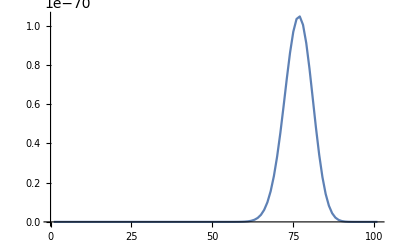

```mathematica
ListLinePlot[dist, PlotRange->All]
```